```mathematica
y[ψ_]:=a √(1-ϵ^2)Sin[ ψ]
```

```mathematica
x[ψ_]:=a(-ϵ+Cos[ ψ])
```

```mathematica
t[ψ_]:=(T (ψ- ϵ*Sin[ ψ]))/(2 π)
```

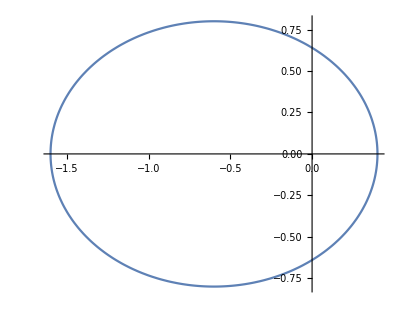

```mathematica
ParametricPlot[{x[ϕ],y[ϕ]}/.{a->1,ϵ->0.6},{ϕ,0,2*Pi}]
```

```mathematica
Planet[a_,r_,ϕ_,τ_,t_]:=Disk[a {Cos[(2 π t)/τ+ϕ],Sin[(2 π t)/τ+ϕ]},r]
```

```mathematica
Animate[Graphics[{Yellow,Planet[0,.25,0,1,t],Brown,Planet[0.387,0.02,0,0.24,t],Orange,Planet[0.723,0.03,0,0.62,t],Blue,Planet[1,0.03,0,1,t]},PlotRange->{{-1.2,1.2},{-1.2,1.2}}],{t,0,1}]
```

```mathematica
1/2+2
```

5/2

```mathematica
(1+5/4)*2*Pi
```

(9 π)/2